## Testpolygon (without import)

{5,5,5}

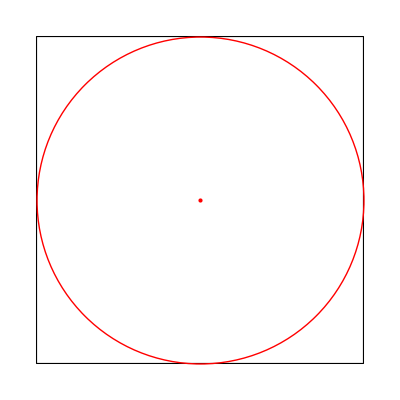

```mathematica
poly = Polygon @ {{0, 0}, {10, 0}, {10, 10}, {0, 10}};
dsk = Disk[{x, y}, r];
sol = Quiet @ ArgMax[{r, RegionWithin[poly, dsk]}, {x, y, r}] 
Graphics[{EdgeForm[Black], FaceForm[White], poly, 
   Red, Circle[Most @ sol, Last @sol], PointSize[Large], Point[Most @ sol]}]
```

## Polygon (with import points from file)

```mathematica
Clear["Global`*"]
data = Drop[Import["polygon.txt", "Table"], -1];
polygon = Polygon @ data;
largestCricle = Disk[{x, y}, r];
pointAndRadius = Quiet @ ArgMax[{r, RegionWithin[polygon, largestCricle]}, {x, y, r}]
Graphics[{EdgeForm[Black], FaceForm[White], polygon, 
   Red, Circle[Most @ pointAndRadius, Last @pointAndRadius], PointSize[Large], Point[Most @ pointAndRadius]}]
```

{472.571,476.664,438.592}

-Graphics-